```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
α[i_]:=Subscript[p, i]/Subscript[ρ, i]^γ
rules={
Subscript[ρ, 2]->(γ+1)/(γ-1+2/M1^2)Subscript[ρ, 1],
Subscript[p, 2]->(2γ M1^2-(γ-1))/(γ+1)Subscript[p, 1]
};
formatRules={M1->Subscript[M, 1]};
```

(1+γ)^(-1-γ) (-1+γ+2/M_1^2)^γ (1+γ (-1+2 M_1^2))

4 (-1+γ) γ (1+γ)^(-1-γ) M_1^(-1-2 γ) (-1+M_1^2)^2 (2+(-1+γ) M_1^2)^(-1+γ)

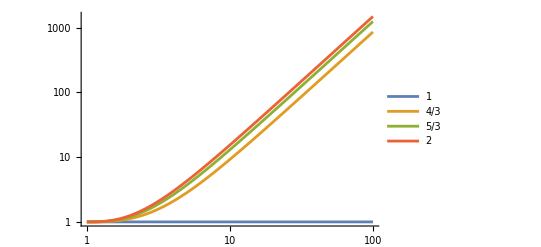

```mathematica
assums={ Subscript[ρ, 1]>0,γ>1,M1>0};
ratio = Simplify[α[2]/α[1]/. rules,assums];
ratio/.formatRules
dRatio=D[ratio,M1];
dRatio=Simplify[dRatio,assums];
dRatio/.formatRules
γs = {1,4/3,5/3,2};
LogLogPlot[
Evaluate[ratio/.γ->γs],{M1,1,100},PlotLegends->γs
]
Export["figures/entropy_ratio.svg",%];
```

```mathematica
massEq:=ρ1 U1==ρ2 U2
momEq:=ρ1 U1^2+p1+B1^2/2==ρ2 U2^2+p2+B2^2/2
energyEq:=(1/2 ρ1 U1^2+f p1+B1^2) U1==(1/2 ρ2 U2^2+f p2 +B2^2) U2
FaradayEq:=B1 U1==B2 U2
eqs={massEq,momEq,energyEq,FaradayEq};
```

```mathematica
rules={
U2->r U1,
f->γ/(γ-1),
Subscript[B, 1]^2->(Subscript[U, 1]^2  Subscript[ρ, 1])/A^2,
p1->(U1^2  ρ1)/(S^2 γ)
};
Simplify[Eliminate[eqs,{B2,ρ2,p2}]/.rules,{U1>0, ρ1>0}]
```

((-1+r) (S^2 (-2+γ-r γ)+A^2 r (-2+S^2 (1+r-γ+r γ))))/(A S (-1+γ))==0

```mathematica
Collect[S^2 (-2+γ-r γ)+A^2 r (-2+S^2 (1+r-γ+r γ))==0,r]
```

-2 S^2+S^2 γ+r (-2 A^2+A^2 S^2-S^2 γ-A^2 S^2 γ)+r^2 (A^2 S^2+A^2 S^2 γ)==0

```mathematica
assums={A>0 ,S>0,γ>1};
Solve[-2 S^2+S^2 γ+r (-2 A^2+A^2 S^2-S^2 γ-A^2 S^2 γ)+r^2 (A^2 S^2+A^2 S^2 γ)==0,{r},Reals,Assumptions->assums]//Simplify
```

{{r→(A^2 (2+S^2 (-1+γ))+S^2 γ-√(A^4 (2+S^2 (-1+γ))^2+S^4 γ^2+A^2 (4 S^2 γ+S^4 (8+2 γ-2 γ^2))))/(2 A^2 S^2 (1+γ))},{r→(A^2 (2+S^2 (-1+γ))+S^2 γ+√(A^4 (2+S^2 (-1+γ))^2+S^4 γ^2+A^2 (4 S^2 γ+S^4 (8+2 γ-2 γ^2))))/(2 A^2 S^2 (1+γ))}}

```mathematica
r1:=1/(2 A^2 S^2 (1+γ))(A^2 (2+S^2 (-1+γ))+S^2 γ+√(A^4 (2+S^2 (-1+γ))^2+S^4 γ^2+A^2 (4 S^2 γ+S^4 (8+2 γ-2 γ^2))))
Simplify[Limit[r1,{A->∞}],assums]
Simplify[Limit[r1,{A->∞,S->∞}],assums]
```

(2+S^2 (-1+γ))/(S^2 (1+γ))

(-1+γ)/(1+γ)

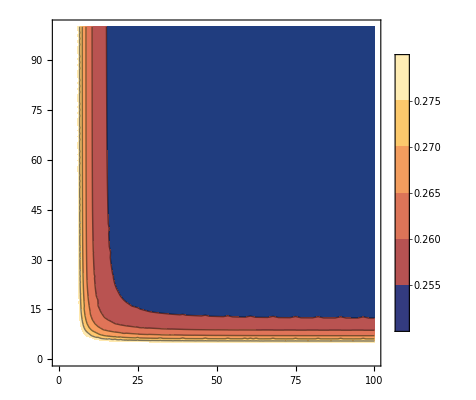
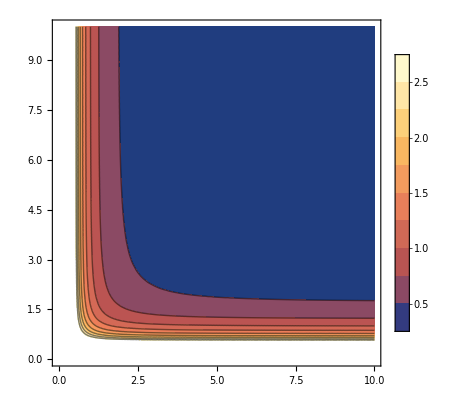

```mathematica
Block[{γ=5/3,p1,p2},
p1=ContourPlot[r1,{A,0,100},{S,0,100},PlotLegends->Automatic];
p2=ContourPlot[r1,{A,0,10},{S,0,10},PlotLegends->Automatic];
Export["figures/shock_U2.svg",p1];
Export["figures/shock_U2_zoom.svg",p2];
{p1,p2}
]
```